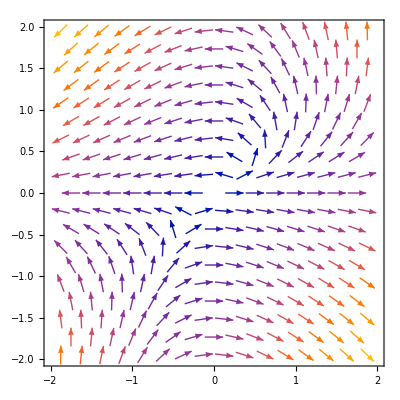

```mathematica
VectorPlot[{x-y,x y},{x,-2,2},{y,-2,2}]
```

```mathematica
(*Al parecer es positiva, ya que va en el sentido de las manecillas del reloj*)
```

```mathematica
Integrate[Dot[{2Cos[t]-2Sin[t],4Cos[t]Sin[t]},{-2Sin[t],2Cos[t]}],{t,0,3Pi/2}]
```

2/3+3 π

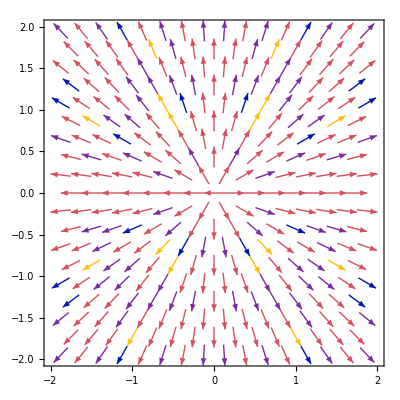

```mathematica
VectorPlot[{x/(Sqrt[x^2+y^2]),y/(Sqrt[x^2+y^2])},{x,-2,2},{y,-2,2}]
```

```mathematica
(*Al parecer es positiva, ya que va en el sentido del campo vectorial*)
```

```mathematica
Integrate[Dot[{x/(Sqrt[x^2+(1+x^2)^2]),(1+x^2)/(Sqrt[x^2+(1+x^2)^2])},{x,1+x^2}],{x,-1,1},Reals]
```

1/(3 √5)ℝ (10+3 ⅈ (-5+√5) EllipticE[ⅈ ArcCsch[1/2 (1+√5)],1/2 (7+3 √5)]-5 ⅈ (-1+√5) EllipticF[ⅈ ArcCsch[1/2 (1+√5)],1/2 (7+3 √5)])

```mathematica
Integrate[Dot[{Exp[(t^2)-1],(t^2)*(t^3)},{2t,3t^2}],{t,0,1}]
```

11/8-1/ⅇ

```mathematica
Integrate[Dot[{2t,t^2,3t},{2,3,-2t}],{t,-1,1}]
```

-2

```mathematica
Integrate[(Exp[-t]*Cos[4t])^3 (Exp[-t]Sin[4t])^2 (Exp[-t])*(Sqrt[(D[Exp[-t]*Cos[4t]])^2+(D[Exp[-t]Sin[4t],t])^2+D[Exp[-t]]^2]),{t,0,2Pi}]
```

$Aborted

```mathematica
Integrate[Dot[{(Sin[t])^2,4(Sin[t]) Cos[t]},{2Cos[t],-2Sin[t]}],{t,0,2Pi}]
```

0